```mathematica
(*for plotting*)
th = 2; asz =16;
```

```mathematica
(*Case 1 from 6 to 8 am. Solar radiation starts from 0 to  0.4kW/m2*)
(*Case 2 from 8 to 10 am. Solar radiation starts from 0.4 to  0.8kW/m2*)
(*Case 3 from 10am to 12 pm. Solar radiation starts from 0.8 to  1.2kW/m2*)

SR1[t_]:= t/(2*3600)* 0.4*1000 ;
SR2[t_]:= 400 +t/(2*3600)* 0.4*1000 ;
SR3[t_]:= 800+ t/(2*3600)* 0.4*1000 ;
```

```mathematica
Te[t_,T0_]:= T0 + 4 t/(2*3600); (*temperature increases linearly by 4degC in 2 hours*)
```

```mathematica
(*ECTOTHERM*)
(*this function finds for a given body size the minimum temperature and the warm-up time*)
findminT[z_,rK1_, rK2_, case_]:=Module[{minT, warmt, Tf,c0 =28, c1 =1.5 ,ε= 0.95, r3 =1,Tmin, Tmax,SR,Tfinal,Tmid,sol},
Tf = c0 + c1*z/2;
Tmin = 0;
Tmax = Tf;
Which[
case==1, SR = SR1,
case ==2 , SR = SR2,
case==3, SR = SR3
];
(*This first one tells in case at 0 deg, warm-up is already possible*)
sol = NDSolve[{ Tth'[t] == 1/(s z/2) (z/2 e 0  +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s z/2) ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2 Kv[z] (Ts[t]- Te[t,Tmin]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,Tmin])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==Tmin},{Tth,Ts},{t,0,2*3600}];

Tfinal = Tth[2*3600]/.sol;

If[Tfinal ≥  Tf, 
minT = 0;
(*ns = NSolve[Tth[t]== Tf/.sol,t];
warmt = (t /.ns[[1]])/3600;*)
Goto[here];
];

(*Do some iteration to find Tmin such that Tfinal <Tf and Tmax such that Tfinal > Tf, warm-up is always guaranteed because Tmin can be close to Tf (= Tmax)*)
While[Abs[Tmin - Tmax]> 0.1,
Tmid = Tmin+ (Tmax -Tmin)/2;
sol = NDSolve[{ Tth'[t] == 1/(s z/2) (z/2 e 0  +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s z/2) ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2 Kv[z] (Ts[t]- Te[t,Tmid]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,Tmid])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==Tmid},{Tth,Ts},{t,0,2*3600}];

Tfinal = Tth[2*3600]/.sol;

If[Tfinal[[1]] <  Tf, 
Tmin = Tmid;
,
Tmax = Tmid;
];
];
minT =Tmin;
(*Quiet[ns = NSolve[Tth[t]== Tf/.sol,t]];
warmt = (t /.ns[[1]])/3600;*)
Label[here];
{z,minT(*,warmt*)}];
```

```mathematica
vect = Flatten[{Range[0.01,0.1,0.01],Range[0.2,2,0.1]}];
```

```mathematica
DATA= {1,2,3};
Do[
data= Table[Table[findminT[z,rK1,rK2,case], {z, vect}],{rK1,{0.2,1,5}},{rK2,{0.2,1,5}}];
DATA[[case]] = data;
,{case,{1,2,3}}]
```

```mathematica
fig = {};
Do[
d1 = ListPlot[DATA[[case,1]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d2 = ListPlot[DATA[[case,2]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d3 = ListPlot[DATA[[case,3]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
AppendTo[fig,{d1,d2,d3}];
,{case,{1,2,3}}];
```

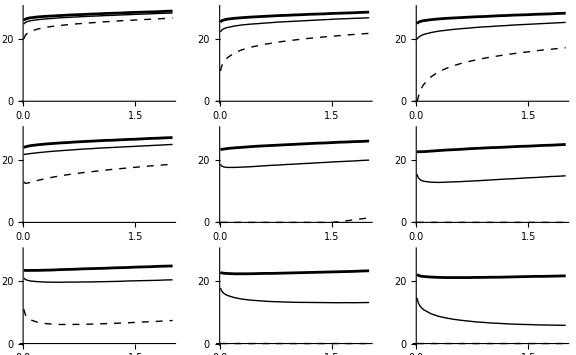

```mathematica
out =GraphicsGrid[Transpose[fig],ImageSize->Large]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\1 Size and range\\12 Appendix warm-up\\fig_analysis\\ecto_min_T.png",out, ImageResolution->200]
```

C:\Users\tramiada\Documents\Projects\1 Size and range\12 Appendix warm-up\fig_analysis\ecto_min_T.png

```mathematica
zz =1 ; ε= 0.95; rK1= 1; r3 =1;T00 = 18.64;
```

```mathematica
sol = NDSolve[{ Tth'[t] == 1/(s zz/2) (zz/2 e 0  +  Ath[zz] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s zz/2) ( - Ath[zz] rK1 Ksth (Ts[t] - Tth[t]) + As[zz] (- Kv[zz] (Ts[t]- Te[t,T00]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,T00])^4 + r3 SR2[t])) ,Tth[0]==Ts[0]==T00},{Tth,Ts},{t,0,2*3600}]
```

{{Tth→InterpolatingFunction[{{0., 7200.}}, <>],Ts→InterpolatingFunction[{{0., 7200.}}, <>]}}

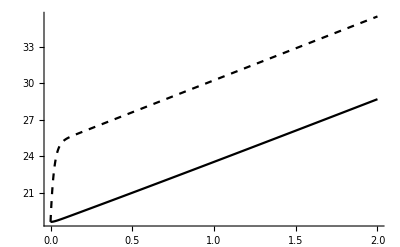

```mathematica
Plot[Evaluate[{Tth[t*3600],Ts[t*3600]}/.sol],{t,0,2},PlotStyle->{Black,{Black,Dashed}}]
```

```mathematica
(*ENDOTHERM*)
(*this function finds for a given body size the minimum temperature and the warm-up time*)
findminT2[z_,rK1_, rK2_, case_]:=Module[{minT, warmt, Tf,c0 =28, c1 =1.5 ,ε= 0.95, r3 =0.,Tmin, Tmax,SR,Tfinal,Tmid,sol},
Tf = c0 + c1*z/2;
Tmin = 0;
Tmax = Tf;
Which[
case==1, SR = SR1,
case ==2 , SR = SR2,
case==3, SR = SR3
];
(*This first one tells in case at 0 deg, warm-up is already possible*)
sol = NDSolve[{ Tth'[t] == 1/(s z/2) (z/2 e 0.1 Tth[t] +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s z/2) ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2 Kv[z] (Ts[t]- Te[t,Tmin]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,Tmin])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==Tmin},{Tth,Ts},{t,0,0.5*3600}];

Tfinal = Tth[0.5*3600]/.sol;

If[Tfinal ≥  Tf, 
minT = 0;
(*ns = NSolve[Tth[t]== Tf/.sol,t];
warmt = (t /.ns[[1]])/3600;*)
Goto[here];
];

(*Do some iteration to find Tmin such that Tfinal <Tf and Tmax such that Tfinal > Tf, warm-up is always guaranteed because Tmin can be close to Tf (= Tmax)*)
While[Abs[Tmin - Tmax]> 0.1,
Tmid = Tmin+ (Tmax -Tmin)/2;
sol = NDSolve[{ Tth'[t] == 1/(s z/2) (z/2 e 0.1 Tth[t]  +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s z/2) ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2 Kv[z] (Ts[t]- Te[t,Tmid]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,Tmid])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==Tmid},{Tth,Ts},{t,0,0.5*3600}];

Tfinal = Tth[0.5*3600]/.sol;

If[Tfinal[[1]] <  Tf, 
Tmin = Tmid;
,
Tmax = Tmid;
];
];
minT =Tmin;
(*Quiet[ns = NSolve[Tth[t]== Tf/.sol,t]];
warmt = (t /.ns[[1]])/3600;*)
Label[here];
{z,minT(*,warmt*)}];
```

```mathematica
DATA= {1,2,3};
Do[
data= Table[Table[findminT2[z,rK1,rK2,case], {z, vect}],{rK1,{0.2,1,5}},{rK2,{0.2,1,5}}];
DATA[[case]] = data;
,{case,{1,2,3}}]
```

```mathematica
fig = {};
Do[
d1 = ListPlot[DATA[[case,1]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d2 = ListPlot[DATA[[case,2]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d3 = ListPlot[DATA[[case,3]],Joined->True,PlotRange-> {All, {0,30}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
AppendTo[fig,{d1,d2,d3}];
,{case,{1,2,3}}];
```

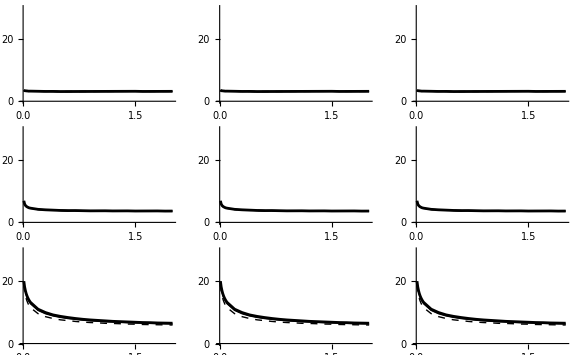

```mathematica
out =GraphicsGrid[Transpose[fig],ImageSize->Large]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\1 Size and range\\12 Appendix warm-up\\fig_analysis\\endo_min_T_aw_0.1_no_SR.png",out, ImageResolution->200]
```

C:\Users\tramiada\Documents\Projects\1 Size and range\12 Appendix warm-up\fig_analysis\endo_min_T_aw_0.1_no_SR.png

```mathematica
(*for warm-up time*)
```

```mathematica
(*ENDOTHERM*)
(*this function finds for a given body size the minimum temperature and the warm-up time*)
findminT2[z_,rK1_, rK2_, case_]:=Module[{minT, warmt, Tf,c0 =28, c1 =1.5 ,ε= 0.95, r3 =1.,Tmin, Tmax,SR,Tfinal,Tmid,sol,ns},
Tf = c0 + c1*z/2;
Tmin = 20;
Tmax = Tf;
Which[
case==1, SR = SR1,
case ==2 , SR = SR2,
case==3, SR = SR3
];
(*This first one tells in case at 0 deg, warm-up is already possible*)
sol = NDSolve[{ Tth'[t] == 1/(s z/2) (z/2 e 0.1 Tth[t] +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s z/2) ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2 Kv[z] (Ts[t]- Te[t,Tmin]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,Tmin])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==Tmin},{Tth,Ts},{t,0,2*3600}];

Tfinal = Tth[2*3600]/.sol;

If[Tfinal[[1]] ≥  Tf, 
(*minT = 0;*)
Quiet[ns = NSolve[Tth[t]== Tf/.sol,t]];
warmt = (t /.ns[[1]])(*/3600*);
,
warmt = 3;
(*Goto[here];*)
];

(*(*Do some iteration to find Tmin such that Tfinal <Tf and Tmax such that Tfinal > Tf, warm-up is always guaranteed because Tmin can be close to Tf (= Tmax)*)
While[Abs[Tmin - Tmax]> 0.1,
Tmid = Tmin+ (Tmax -Tmin)/2;
sol = NDSolve[{ Tth'[t] == 1/(s z/2) (z/2 e 0.1 Tth[t]  +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s z/2) ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2 Kv[z] (Ts[t]- Te[t,Tmid]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,Tmid])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==Tmid},{Tth,Ts},{t,0,0.5*3600}];

Tfinal = Tth[0.5*3600]/.sol;

If[Tfinal[[1]] <  Tf, 
Tmin = Tmid;
,
Tmax = Tmid;
];
];
minT =Tmin;
Quiet[ns = NSolve[Tth[t]== Tf/.sol,t]];
warmt = (t /.ns[[1]])/3600;
Label[here];*)
{z,(*minT,*)warmt}];
```

```mathematica
DATA= {1,2,3};
Do[
data= Table[Table[findminT2[z,rK1,rK2,case], {z, vect}],{rK1,{0.2,1,5}},{rK2,{0.2,1,5}}];
DATA[[case]] = data;
,{case,{1,2,3}}]
```

```mathematica
(*for plotting*)
th = 2; asz =12;
fig = {};
Do[
d1 = ListPlot[DATA[[case,1]],Joined->True,PlotRange-> {All, All},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d2 = ListPlot[DATA[[case,2]],Joined->True,PlotRange-> {All, All},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d3 = ListPlot[DATA[[case,3]],Joined->True,PlotRange-> {All, All},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
AppendTo[fig,{d1,d2,d3}];
,{case,{1,2,3}}];
```

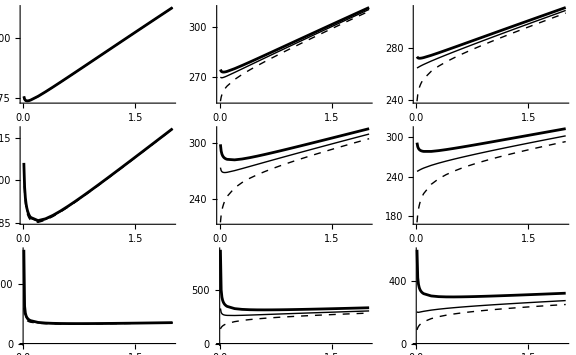

```mathematica
out =GraphicsGrid[Transpose[fig],ImageSize->Large]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\1 Size and range\\12 Appendix warm-up\\fig_analysis\\endo_time_aw_0.1.png",out, ImageResolution->200]
```

C:\Users\tramiada\Documents\Projects\1 Size and range\12 Appendix warm-up\fig_analysis\endo_time_aw_0.1.png

```mathematica
(*ECTOTHERM*)
(*this function finds for a given body size the minimum temperature and the warm-up time*)
findminT[z_,rK1_, rK2_, case_]:=Module[{minT, warmt, Tf,c0 =28, c1 =1.5 ,ε= 0.95, r3 =1.,Tmin, Tmax,SR,Tfinal,Tmid,sol,ns},
Tf = c0 + c1*z/2;
Tmin =35;
Tmax = Tf;
Which[
case==1, SR = SR1,
case ==2 , SR = SR2,
case==3, SR = SR3
];
(*This first one tells in case at 0 deg, warm-up is already possible*)
sol = NDSolve[{ Tth'[t] == 1/(s z/2) (z/2 e 0 (*0.1 Tth[t]*) +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s z/2) ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2 Kv[z] (Ts[t]- Te[t,Tmin]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,Tmin])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==Tmin},{Tth,Ts},{t,0,5*3600}];

Tfinal = Tth[5*3600]/.sol;

If[Tfinal[[1]] ≥  Tf, 
(*minT = 0;*)
Quiet[ns = NSolve[Tth[t]== Tf/.sol,t]];
warmt = (t /.ns)[[1]](*/3600*);
,
warmt = 5*3600;
(*Goto[here];*)
];

(*(*Do some iteration to find Tmin such that Tfinal <Tf and Tmax such that Tfinal > Tf, warm-up is always guaranteed because Tmin can be close to Tf (= Tmax)*)
While[Abs[Tmin - Tmax]> 0.1,
Tmid = Tmin+ (Tmax -Tmin)/2;
sol = NDSolve[{ Tth'[t] == 1/(s z/2) (z/2 e 0.1 Tth[t]  +  Ath[z] rK1 Ksth (Ts[t] - Tth[t])), Ts'[t] ==  1/(s z/2) ( - Ath[z] rK1 Ksth (Ts[t] - Tth[t]) + As[z] (- rK2 Kv[z] (Ts[t]- Te[t,Tmid]) - σ ε (273 + Ts[t])^4 + σ ε (273 + Te[t,Tmid])^4 + r3 SR[t])) ,Tth[0]==Ts[0]==Tmid},{Tth,Ts},{t,0,0.5*3600}];

Tfinal = Tth[0.5*3600]/.sol;

If[Tfinal[[1]] <  Tf, 
Tmin = Tmid;
,
Tmax = Tmid;
];
];
minT =Tmin;
Quiet[ns = NSolve[Tth[t]== Tf/.sol,t]];
warmt = (t /.ns[[1]])/3600;
Label[here];*)
{z,(*minT,*)warmt}];
```

```mathematica
findminT[1,1,1,1]
```

{1,InverseFunction[InterpolatingFunction[{{0., 18000.}}, <>],1,1][28.75]}

```mathematica
Tth[1] /.ss
```

{28.}

```mathematica
{{Tth->InterpolatingFunction[{{0., 18000.}}, <>],Ts->InterpolatingFunction[{{0., 18000.}}, <>]}}
```

General::noinfo: Input expression InterpolatingFunction[{{0., 18000.}}, <>] contains insufficient information to interpret the result.

```mathematica
vect = Flatten[{Range[0.01,0.1,0.01],Range[0.2,2,0.1]}];
DATA= {1,2,3};
Do[
data= Table[Table[findminT[z,rK1,rK2,case], {z, vect}],{rK1,{0.2,1,5}},{rK2,{0.2,1,5}}];
DATA[[case]] = data;
,{case,{1,2,3}}]
```

```mathematica
(*for plotting*)
th = 2; asz =12;
fig = {};
Do[
d1 = ListPlot[DATA[[case,1]],Joined->True,PlotRange-> {All, {0,All}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d2 = ListPlot[DATA[[case,2]],Joined->True,PlotRange-> {All, {0,All}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
d3 = ListPlot[DATA[[case,3]],Joined->True,PlotRange-> {All, {0,All}},PlotStyle->{{Black,Dashed,AbsoluteThickness[th-1]}, {Black,AbsoluteThickness[th-1]},{AbsoluteThickness[th],Black}},AxesStyle->Directive[asz,AbsoluteThickness[th-1],Black],ImageSize->Medium];
AppendTo[fig,{d1,d2,d3}];
,{case,{1,2,3}}];
```

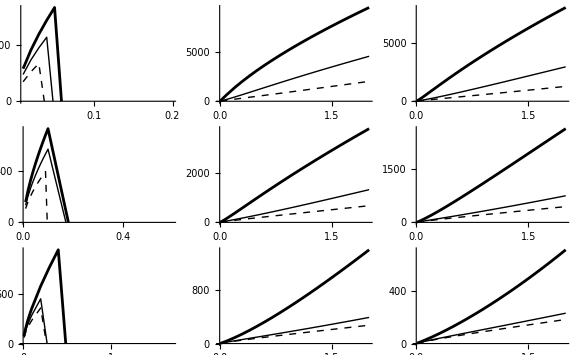

```mathematica
out =GraphicsGrid[Transpose[fig],ImageSize->Large]
```

```mathematica
Export["C:\\Users\\tramiada\\Documents\\Projects\\1 Size and range\\12 Appendix warm-up\\fig_analysis\\ecto_time.png",out, ImageResolution->200]
```

C:\Users\tramiada\Documents\Projects\1 Size and range\12 Appendix warm-up\fig_analysis\endo_time_aw_0.1.png

```mathematica
50*44
```

2200